# S8.2 check

## Alternative exogenous reoccupation dynamics

## Plotting style

```mathematica
TextSize=16;
TicksSize=16;
GraphThickness=0.02;
LinesThickness=0.01;
MarkerThickness=1/35;
opacity=1;
size=320;
```

```mathematica
FinalColors=ResourceFunction["HexToColor"]/@{"#9B536D","#7F9E5D","#56AAFF"};
```

```mathematica
FinalColors
```

{RGBColor[0.6078431372549019, 0.3254901960784314, 0.42745098039215684],RGBColor[0.4980392156862745, 0.6196078431372549, 0.36470588235294116],RGBColor[0.33725490196078434, 0.6666666666666666, 1.]}

```mathematica
Viridis=ResourceFunction["HexToColor"]/@{"#440154","#482475","#414487","#355f8d","#2a788e","#21918c","#22a884","#44bf70","#7ad151","#bddf26","#fde725"}
```

{RGBColor[0.26666666666666666, 0.00392156862745098, 0.32941176470588235],RGBColor[0.2823529411764706, 0.1411764705882353, 0.4588235294117647],RGBColor[0.2549019607843137, 0.26666666666666666, 0.5294117647058824],RGBColor[0.20784313725490194, 0.37254901960784315, 0.5529411764705883],RGBColor[0.16470588235294117, 0.47058823529411764, 0.5568627450980392],RGBColor[0.12941176470588234, 0.5686274509803921, 0.5490196078431373],RGBColor[0.13333333333333333, 0.6588235294117647, 0.5176470588235293],RGBColor[0.26666666666666666, 0.7490196078431373, 0.4392156862745098],RGBColor[0.4784313725490196, 0.8196078431372549, 0.3176470588235294],RGBColor[0.7411764705882353, 0.8745098039215686, 0.14901960784313725],RGBColor[0.9921568627450981, 0.9058823529411765, 0.14509803921568626]}

```mathematica
viridisGradient=Blend[Viridis,#]&;
```

```mathematica
ViridisColors=Reverse[Table[viridisGradient[i/12],{i,0,12}]]
```

{RGBColor[0.9921568627450981, 0.9058823529411765, 0.14509803921568626],RGBColor[0.7830065359477124, 0.8797385620915033, 0.14836601307189543],RGBColor[0.5660130718954248, 0.8379084967320262, 0.261437908496732],RGBColor[0.37254901960784315, 0.7843137254901961, 0.3784313725490196],RGBColor[0.2222222222222222, 0.7189542483660131, 0.46535947712418296],RGBColor[0.1326797385620915, 0.6437908496732025, 0.522875816993464],RGBColor[0.12941176470588234, 0.5686274509803921, 0.5490196078431373],RGBColor[0.1588235294117647, 0.4869281045751634, 0.5555555555555556],RGBColor[0.19346405228758168, 0.40522875816993464, 0.5542483660130719],RGBColor[0.23137254901960783, 0.3196078431372549, 0.5411764705882354],RGBColor[0.26405228758169935, 0.22483660130718952, 0.5058823529411764],RGBColor[0.2797385620915033, 0.11830065359477124, 0.4372549019607843],RGBColor[0.26666666666666666, 0.00392156862745098, 0.32941176470588235]}

## Check

## Eq. (6)

### Steady-state solution

```mathematica
eqR0=0==-ω R-(σ k1)/H R*V+κ W+(γ k2)/H R*V+r V
```

0==r V+(k2 R V γ)/H+W κ-(k1 R V σ)/H-R ω

```mathematica
eqW0=0==ω R+(σ k1)/H R*V-κ W-v W
```

0==-v W-W κ+(k1 R V σ)/H+R ω

```mathematica
eqV0=0==v W-(γ k2)/H R*V-r V
```

0==-r V+v W-(k2 R V γ)/H

```mathematica
eqH0=H==R+W+V
```

H==R+V+W

```mathematica
steadyStateAll=Solve[{eqR0,eqW0,eqV0,eqH0},{R,W,V}];
```

```mathematica
steadyStateSol=steadyStateAll[[1]];
```

### Numerical solution

```mathematica
params={ω->0.066,κ->0.239,v->0.026,k1->6,k2->7,σ->0.068,γ->0.025,r->0.05}
```

{ω→0.066,κ→0.239,v→0.026,k1→6,k2→7,σ→0.068,γ→0.025,r→0.05}

```mathematica
γ*k2*(1+κ/v)-σ k1/.params
```

1.37565

```mathematica
initials={R[0]==81000,W[0]==9000,V[0]==10000}
```

{R[0]==81000,W[0]==9000,V[0]==10000}

```mathematica
eqR=D[R[t],t]==-ω R[t]-(σ k1)/H[t] R[t] V[t]+κ W[t]+(γ k2)/H[t] R[t] V[t]+r V[t];
eqW=D[W[t],t]==ω R[t]+(σ k1)/H[t] R[t] V[t]-κ W[t]-v W[t];
eqV=D[V[t],t]==v W[t]-(γ k2)/H[t] R[t] V[t]-r V[t];
eqH=H[t]==R[t]+W[t]+V[t];
```

```mathematica
{Rss,Wss,Vss}=Values[steadyStateSol/. H->Total[initials[[All,2]]]/. params]//N
```

{74549.3,22245.7,3205.05}

```mathematica
sol=NDSolve[{eqR,eqW,eqV,eqH,initials,H[0]==Total[initials[[All,2]]]}/. params,{R[t],W[t],V[t],H[t]},{t,0,100}];
```

### Plotting the model

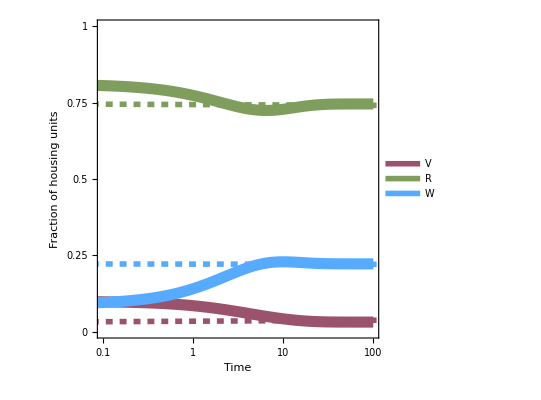

```mathematica
SteadyStatePlot=LogLinearPlot[Evaluate[{V[t]/Total[initials[[All,2]]],R[t]/Total[initials[[All,2]]],W[t]/Total[initials[[All,2]]]}/. sol],{t,0.001,100},PlotRange->{{10^-1,100},{0,1}},PlotStyle->(Directive[#,Thickness[GraphThickness]]&/@FinalColors),Frame->True,AspectRatio->1,PlotLegends->{"V","R","W"},FrameLabel->{Style["Time",TextSize,FontFamily->"Arial"],Style["Fraction of housing units",TextSize,FontFamily->"Arial"]},FrameTicks->{{{0,0.25,0.50,0.75,1},None},{Table[{10^i,Superscript[10,i]},{i,-1,3}],None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.5LinesThickness]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],Epilog->{{Dashed,Thickness[LinesThickness],FinalColors[[1]],Line[{{-4,Vss/Total[initials[[All,2]]]},{1000,Rss/Total[initials[[All,2]]]}}]},{Dashed,Thickness[LinesThickness],FinalColors[[2]],Line[{{-4,Rss/Total[initials[[All,2]]]},{1000,Wss/Total[initials[[All,2]]]}}]},{Dashed,Thickness[LinesThickness],FinalColors[[3]],Line[{{-4,Wss/Total[initials[[All,2]]]},{1000,Vss/Total[initials[[All,2]]]}}]}}]
```

### Scaling of R

```mathematica
paramsScaling={ω->0.066,κ->0.239,v->0.026,σ->0.068,γ->0.025,r->0.05,H->n,δ2->7/6,δ1->8/7,E0->1}
```

{ω→0.066,κ→0.239,v→0.026,σ→0.068,γ→0.025,r→0.05,H→n,δ2→7/6,δ1→8/7,E0→1}

```mathematica
RSteadyState=R/.steadyStateSol
```

(H r v-H k2 v γ+H r κ-H k2 γ κ+H k1 v σ+H r ω+H v ω-√((-H r v+H k2 v γ-H r κ+H k2 γ κ-H k1 v σ-H r ω-H v ω)^2-4 (H^2 r v+H^2 r κ) (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))

```mathematica
RSteadyStateSimp=Assuming[ω>0&&κ>0&&v>0&&k1>0&&k2>0&&σ>0&&γ>0&&r>0,FullSimplify[RSteadyState]]
```

(H (-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))-√(H^2 (4 r (v+κ) (-k1 v σ+k2 γ (v+κ+ω))+(-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))^2)))/(2 k1 v σ-2 k2 γ (v+κ+ω))

```mathematica
RScaling=RSteadyStateSimp/.{k1->E0 n^(δ1-1),k2->E0 n^(δ2-1)}
```

1/(2 E0 n^(-1+δ1) v σ-2 E0 n^(-1+δ2) γ (v+κ+ω))(H (-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))-√(H^2 (4 r (v+κ) (-E0 n^(-1+δ1) v σ+E0 n^(-1+δ2) γ (v+κ+ω))+(-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))^2)))

```mathematica
Assuming[δ2>δ1,Asymptotic[RScaling,n->∞]]
```

1/(2 E0 n^(-1+δ1) v σ-2 E0 n^(-1+δ2) γ (v+κ+ω))(H (-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))-√(H^2 (4 r (v+κ) (-E0 n^(-1+δ1) v σ+E0 n^(-1+δ2) γ (v+κ+ω))+(-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))^2)))

```mathematica
RScalingDenominator=-Denominator[RScaling]
```

-2 E0 n^(-1+δ1) v σ+2 E0 n^(-1+δ2) γ (v+κ+ω)

```mathematica
RScalingNumerator=-Numerator[RScaling]
```

-H (-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))+√(H^2 (4 r (v+κ) (-E0 n^(-1+δ1) v σ+E0 n^(-1+δ2) γ (v+κ+ω))+(-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))^2))

```mathematica
RScalingAsymptotics=FullSimplify[(2E0 n^(-1+δ2) γ (v+κ)H)/(2 E0 n^(-1+δ2) γ (v+κ+ω))/.H->n]
```

(n (v+κ))/(v+κ+ω)

```mathematica
ExactModelR=RScaling/.paramsScaling
```

((0.01655+0.026 (0.066+0.068 n^(1/7))-0.006625 n^(1/6)) n-√(((0.01655+0.026 (0.066+0.068 n^(1/7))-0.006625 n^(1/6))^2+0.053 (-0.001768 n^(1/7)+0.008275 n^(1/6))) n^2))/(0.003536 n^(1/7)-0.01655 n^(1/6))

```mathematica
Asymptotic[ExactModelR,n->∞]
```

0.800604 n

```mathematica
Series[ExactModelR,{n,∞,0}]
```

0.800604 n-0.042602 n^(41/42)-0.00910216 n^(20/21)-0.00194473 n^(13/14)-0.000415502 n^(19/21)-0.0000887743 n^(37/42)-0.0000189671 n^(6/7)-0.207376 n^(5/6)+0.0621177 n^(17/21)+0.0416731 n^(11/14)+0.0164831 n^(16/21)+0.00554441 n^(31/42)+0.00172439 n^(5/7)+0.000512479 n^(29/42)+0.518186 n^(2/3)+0.0106763 n^(9/14)-0.102156 n^(13/21)-0.0742189 n^(25/42)-0.0373908 n^(4/7)-0.0160195 n^(23/42)-0.00624714 n^(11/21)-1.16222 √n-0.47189 n^(10/21)+0.0631908 n^(19/42)+0.199636 n^(3/7)+0.161157 n^(17/42)+0.0952652 n^(8/21)+0.0480437 n^(5/14)+2.28392 n^(1/3)+2.03401 n^(13/42)+0.744538 n^(2/7)-0.139001 n^(11/42)-0.424452 n^(5/21)-0.386022 n^(3/14)-0.258904 n^(4/21)-3.7115 n^(1/6)-5.84206 n^(1/7)-4.43487 n^(5/42)-1.77636 n^(2/21)+0.143776 n^(1/14)+0.926583 n^(1/21)+0.970579 n^(1/42)+4.10009+12.158 (1/n)^(1/42)+15.3531 (1/n)^(1/21)+11.6154 (1/n)^(1/14)+5.35213 (1/n)^(2/21)+0.455831 (1/n)^(5/42)-1.95275 (1/n)^(1/7)+1.14019 (1/n)^(1/6)-14.5019 (1/n)^(4/21)-36.23 (1/n)^(3/14)-43.4487 (1/n)^(5/21)-34.0085 (1/n)^(11/42)-17.8946 (1/n)^(2/7)+O[1/n]^(13/42)

```mathematica
AsymptoticsModelR=RScalingAsymptotics/.params
```

0.800604 n

```mathematica
RValues=10.0^Range[1,8,7/14];
```

```mathematica
RValues=RValues[[2;;-2]]
```

{31.6228,100.,316.228,1000.,3162.28,10000.,31622.8,100000.,316228.,1.×10^6,3.16228×10^6,1.×10^7,3.16228×10^7}

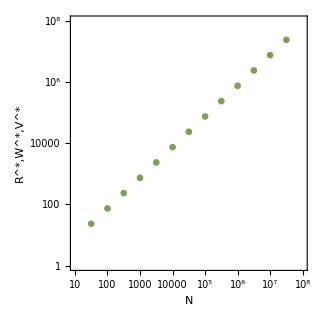

```mathematica
RScalingModelPlot=ListLogLogPlot[Table[{RValues[[i]],ExactModelR/.n->RValues[[i]]},{i,1,Length[RValues]}],PlotRange->{{10^1,10^8},{10^0,10^8}},PlotMarkers->{Graphics[{FaceForm[FinalColors[[2]]],EdgeForm[{FinalColors[[2]],Opacity[opacity]}], Disk[]}],MarkerThickness},Frame->True,AspectRatio->1,FrameLabel->{Style["N",TextSize,FontFamily->"Arial"],Style["R^*,W^*,V^*",TextSize,FontFamily->"Arial"]},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-2,8}],None},{Table[{10^i,Superscript[10,i]},{i,-2,8}],None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.5LinesThickness]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],ImageSize->size]
```

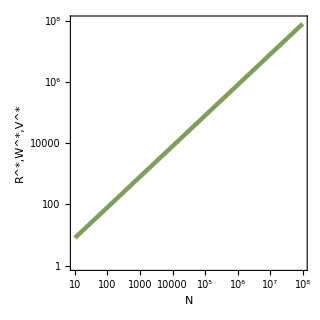

```mathematica
RScalingTheoryPlot=LogLogPlot[AsymptoticsModelR,{n,10^1,10^8},PlotRange->{{10^1,10^8},{10^0,10^8}},PlotStyle->{FinalColors[[2]],Thickness[GraphThickness/2]},Frame->True,AspectRatio->1,FrameLabel->{Style["N",TextSize,FontFamily->"Arial"],Style["R^*,W^*,V^*",TextSize,FontFamily->"Arial"]},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-2,8}],None},{Table[{10^i,Superscript[10,i]},{i,-2,8}],None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.5LinesThickness]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],ImageSize->size]
```

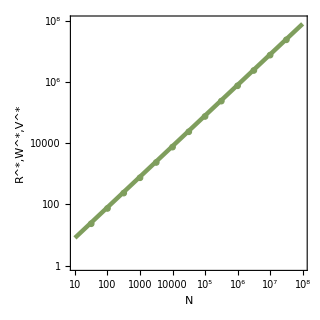

```mathematica
RPlot=Show[RScalingModelPlot,RScalingTheoryPlot]
```

### Scaling of W

```mathematica
WSteadyState=W/.steadyStateSol
```

1/(k2 v γ+k2 γ κ-k1 r σ-k1 v σ)(-H k1 r σ+(H k1 r^2 v σ)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k1 k2 r v γ σ)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k1 r^2 κ σ)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k1 k2 r γ κ σ)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k1^2 r v σ^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 r v γ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k2^2 v γ^2 ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 r γ κ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k2^2 γ^2 κ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k1 r^2 σ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k1 r v σ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k1 k2 v γ σ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 r γ ω^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 v γ ω^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(k1 r σ √((-H r v+H k2 v γ-H r κ+H k2 γ κ-H k1 v σ-H r ω-H v ω)^2-4 (H^2 r v+H^2 r κ) (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(k2 γ ω √((-H r v+H k2 v γ-H r κ+H k2 γ κ-H k1 v σ-H r ω-H v ω)^2-4 (H^2 r v+H^2 r κ) (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))

```mathematica
WSteadyStateSimp=Assuming[ω>0&&κ>0&&v>0&&k1>0&&k2>0&&σ>0&&γ>0&&r>0,FullSimplify[WSteadyState]]
```

((k1 r σ+k2 γ ω) √(H^2 (((r+k2 γ) (v+κ)-k1 v σ)^2+2 ((r (r+v)+k2 (r-v) γ) (v+κ)+k1 v (r+v) σ) ω+(r+v)^2 ω^2))+H (k1 r σ (-((r+k2 γ) (v+κ))+k1 v σ)-(k2 γ (r-k2 γ) (v+κ)+k1 (r (r+v)+k2 (2 r+v) γ) σ) ω-k2 (r+v) γ ω^2))/(2 (k2 γ (v+κ)-k1 (r+v) σ) (-k1 v σ+k2 γ (v+κ+ω)))

```mathematica
WScaling=WSteadyStateSimp/.{k1->E0 n^(δ1-1),k2->E0 n^(δ2-1)}
```

((E0 n^(-1+δ1) r σ+E0 n^(-1+δ2) γ ω) √(H^2 (((r+E0 n^(-1+δ2) γ) (v+κ)-E0 n^(-1+δ1) v σ)^2+2 ((r (r+v)+E0 n^(-1+δ2) (r-v) γ) (v+κ)+E0 n^(-1+δ1) v (r+v) σ) ω+(r+v)^2 ω^2))+H (E0 n^(-1+δ1) r σ (-((r+E0 n^(-1+δ2) γ) (v+κ))+E0 n^(-1+δ1) v σ)-(E0 n^(-1+δ2) γ (r-E0 n^(-1+δ2) γ) (v+κ)+E0 n^(-1+δ1) (r (r+v)+E0 n^(-1+δ2) (2 r+v) γ) σ) ω-E0 n^(-1+δ2) (r+v) γ ω^2))/(2 (E0 n^(-1+δ2) γ (v+κ)-E0 n^(-1+δ1) (r+v) σ) (-E0 n^(-1+δ1) v σ+E0 n^(-1+δ2) γ (v+κ+ω)))

```mathematica
Assuming[δ2>δ1,Asymptotic[WScaling,n->∞]]
```

ConditionalExpression[(ⅇ^(-((-1+δ2) Log[n])+1/2 (2 (-1+δ2) Log[n]+Log[E0^2 H^2 γ^2 (v+κ)^2])) E0 γ ω+E0^2 H γ^2 (v+κ) ω)/(2 E0^2 γ^2 (v+κ) (v+κ+ω)), ]

```mathematica
WScalingAsymptotics=FullSimplify[(E0 H γ (v+κ)E0 γ ω+E0^2 H γ^2 (v+κ) ω)/(2 E0^2 γ^2 (v+κ) (v+κ+ω))/.H->n]
```

(n ω)/(v+κ+ω)

```mathematica
ExactModelW=WScaling/.paramsScaling
```

((-0.066 (0.068 (0.0038+0.00315 n^(1/6)) n^(1/7)+0.006625 (0.05-0.025 n^(1/6)) n^(1/6))+0.0034 (-0.265 (0.05+0.025 n^(1/6))+0.001768 n^(1/7)) n^(1/7)-8.2764×10^-6 n^(1/6)) n+(0.0034 n^(1/7)+0.00165 n^(1/6)) √((0.0000251603+(0.265 (0.05+0.025 n^(1/6))-0.001768 n^(1/7))^2+0.132 (0.265 (0.0038+0.0006 n^(1/6))+0.000134368 n^(1/7))) n^2))/(2 (-0.005168 n^(1/7)+0.006625 n^(1/6)) (-0.001768 n^(1/7)+0.008275 n^(1/6)))

```mathematica
Asymptotic[ExactModelW,n->∞]
```

0.199396 n

```mathematica
Series[ExactModelW,{n,∞,0}]
```

0.199396 n+0.042602 n^(41/42)+0.00910216 n^(20/21)+0.00194473 n^(13/14)+0.000415502 n^(19/21)+0.0000887743 n^(37/42)+0.0000189671 n^(6/7)-0.0516432 n^(5/6)-0.131242 n^(17/21)-0.0601201 n^(11/14)-0.021406 n^(16/21)-0.00685817 n^(31/42)-0.00207499 n^(5/7)-0.000606043 n^(29/42)+0.128848 n^(2/3)+0.369107 n^(9/14)+0.267968 n^(13/21)+0.138123 n^(25/42)+0.0603444 n^(4/7)+0.0238941 n^(23/42)+0.00886199 n^(11/21)-0.285753 √n-0.936899 n^(10/21)-0.957291 n^(19/42)-0.664609 n^(3/7)-0.375853 n^(17/42)-0.18676 n^(8/21)-0.0848304 n^(5/14)+0.527307 n^(1/3)+2.09005 n^(13/42)+2.8597 n^(2/7)+2.57826 n^(11/42)+1.83419 n^(5/21)+1.11683 n^(3/14)+0.608623 n^(4/21)-0.582474 n^(1/6)-3.81415 n^(1/7)-7.07805 n^(5/42)-8.23984 n^(2/21)-7.30353 n^(1/14)-5.39275 n^(1/21)-3.48949 n^(1/42)-1.2028+4.19396 (1/n)^(1/42)+13.335 (1/n)^(1/21)+21.1745 (1/n)^(1/14)+23.8118 (1/n)^(2/21)+21.4353 (1/n)^(5/42)+16.4687 (1/n)^(1/7)+12.1287 (1/n)^(1/6)+6.43464 (1/n)^(4/21)-11.4463 (1/n)^(3/14)-38.3436 (1/n)^(5/21)-60.6792 (1/n)^(11/42)-69.2445 (1/n)^(2/7)+O[1/n]^(13/42)

```mathematica
AsymptoticsModelW=WScalingAsymptotics/.params
```

0.199396 n

```mathematica
WValues=10.0^Range[1,8,7/14];
```

```mathematica
WValues=WValues[[2;;-2]]
```

{31.6228,100.,316.228,1000.,3162.28,10000.,31622.8,100000.,316228.,1.×10^6,3.16228×10^6,1.×10^7,3.16228×10^7}

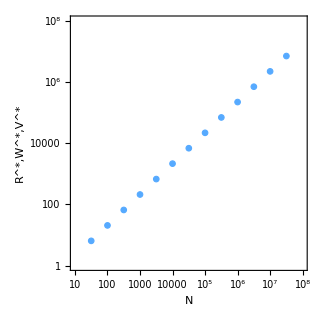

```mathematica
WScalingModelPlot=ListLogLogPlot[Table[{WValues[[i]],ExactModelW/.n->WValues[[i]]},{i,1,Length[WValues]}],PlotRange->{{10^1,10^8},{10^0,10^8}},PlotMarkers->{Graphics[{FaceForm[FinalColors[[3]]],EdgeForm[{FinalColors[[3]],Opacity[opacity]}], Disk[]}],MarkerThickness},Frame->True,AspectRatio->1,FrameLabel->{Style["N",TextSize,FontFamily->"Arial"],Style["R^*,W^*,V^*",TextSize,FontFamily->"Arial"]},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-2,8}],None},{Table[{10^i,Superscript[10,i]},{i,-2,8}],None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.5LinesThickness]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],ImageSize->size]
```

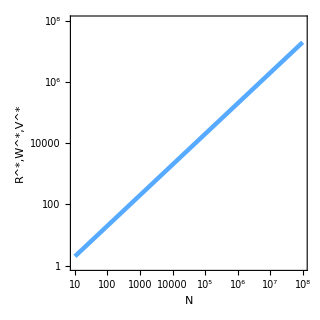

```mathematica
WScalingTheoryPlot=LogLogPlot[AsymptoticsModelW,{n,10^1,10^8},PlotRange->{{10^1,10^8},{10^0,10^8}},PlotStyle->{FinalColors[[3]],Thickness[GraphThickness/2]},Frame->True,AspectRatio->1,FrameLabel->{Style["N",TextSize,FontFamily->"Arial"],Style["R^*,W^*,V^*",TextSize,FontFamily->"Arial"]},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-2,8}],None},{Table[{10^i,Superscript[10,i]},{i,-2,8}],None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.5LinesThickness]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],ImageSize->size]
```

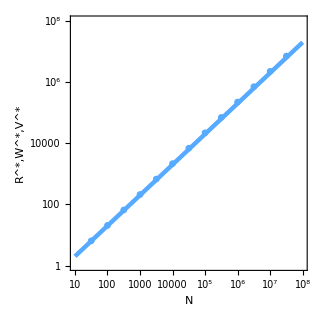

```mathematica
WPlot=Show[WScalingModelPlot,WScalingTheoryPlot]
```

### Scaling of V

```mathematica
VSteadyState=V/.steadyStateSol
```

1/(-k2 v γ-k2 γ κ+k1 r σ+k1 v σ)(-H k2 v γ-H k2 γ κ+H k1 v σ+(H k2 r v^2 γ)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k2^2 v^2 γ^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 r v γ κ)/(-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)-(H k2^2 v γ^2 κ)/(-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)+(H k2 r γ κ^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k2^2 γ^2 κ^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k1 r v^2 σ)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k1 k2 v^2 γ σ)/(-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)-(H k1 r v κ σ)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k1 k2 v γ κ σ)/(-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)-(H k1^2 v^2 σ^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 r v γ ω)/(-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)+(H k2 v^2 γ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k2^2 v γ^2 ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 r γ κ ω)/(-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)+(H k2 v γ κ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k2^2 γ^2 κ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k1 r v σ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(H k1 v^2 σ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k1 k2 v γ σ ω)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 r γ ω^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(H k2 v γ ω^2)/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(k2 v γ √((-H r v+H k2 v γ-H r κ+H k2 γ κ-H k1 v σ-H r ω-H v ω)^2-4 (H^2 r v+H^2 r κ) (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(k2 γ κ √((-H r v+H k2 v γ-H r κ+H k2 γ κ-H k1 v σ-H r ω-H v ω)^2-4 (H^2 r v+H^2 r κ) (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))+(k1 v σ √((-H r v+H k2 v γ-H r κ+H k2 γ κ-H k1 v σ-H r ω-H v ω)^2-4 (H^2 r v+H^2 r κ) (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω))-(k2 γ ω √((-H r v+H k2 v γ-H r κ+H k2 γ κ-H k1 v σ-H r ω-H v ω)^2-4 (H^2 r v+H^2 r κ) (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))/(2 (-k2 v γ-k2 γ κ+k1 v σ-k2 γ ω)))

```mathematica
VSteadyStateSimp=Assuming[ω>0&&κ>0&&v>0&&k1>0&&k2>0&&σ>0&&γ>0&&r>0,FullSimplify[VSteadyState]]
```

(H (k2 γ (v+κ)+r (v+κ+ω)+v (-k1 σ+ω))-√(H^2 (4 r (v+κ) (-k1 v σ+k2 γ (v+κ+ω))+(-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))^2)))/(2 k2 γ (v+κ)-2 k1 (r+v) σ)

```mathematica
VScaling=VSteadyStateSimp/.{k1->E0 n^(δ1-1),k2->E0 n^(δ2-1)}
```

1/(2 E0 n^(-1+δ2) γ (v+κ)-2 E0 n^(-1+δ1) (r+v) σ)(H (E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (-E0 n^(-1+δ1) σ+ω))-√(H^2 (4 r (v+κ) (-E0 n^(-1+δ1) v σ+E0 n^(-1+δ2) γ (v+κ+ω))+(-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))^2)))

```mathematica
Assuming[δ2>δ1,Asymptotic[VScaling,n->∞]]
```

1/(2 E0 n^(-1+δ2) γ (v+κ)-2 E0 n^(-1+δ1) (r+v) σ)(H (E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (-E0 n^(-1+δ1) σ+ω))-√(H^2 (4 r (v+κ) (-E0 n^(-1+δ1) v σ+E0 n^(-1+δ2) γ (v+κ+ω))+(-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))^2)))

```mathematica
1/(2 E0 n^(-1+δ2) γ (v+κ)-2 E0 n^(-1+δ1) (r+v) σ)(H (E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (-E0 n^(-1+δ1) σ+ω))-√(H^2 (4 r (v+κ) (-E0 n^(-1+δ1) v σ+E0 n^(-1+δ2) γ (v+κ+ω))+(-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))^2)))
```

1/(2 E0 n^(-1+δ2) γ (v+κ)-2 E0 n^(-1+δ1) (r+v) σ)(H (E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (-E0 n^(-1+δ1) σ+ω))-√(H^2 (4 r (v+κ) (-E0 n^(-1+δ1) v σ+E0 n^(-1+δ2) γ (v+κ+ω))+(-E0 n^(-1+δ2) γ (v+κ)+r (v+κ+ω)+v (E0 n^(-1+δ1) σ+ω))^2)))

Denominator:
2 E0 n^(-1+δ2) γ (v+κ)-2 E0 n^(-1+δ1) (r+v) σ -> 2 E0 n^(-1+δ2) γ (v+κ)

Numerator:
x1=E0 n^(-1+δ2) γ (v+κ)
x2=E0 n^(-1+δ1) σ
x3=4 r (v+κ) (-v x2+x1 (v+κ+ω)/(v+κ))+(-x1+r (v+κ+ω)+v (x2+ω))^2

Numerator=n(x1+r (v+κ+ω)-v x2+v ω-√x3)

C=r (v+κ+ω)+v ω
x4=v x2

x3=4 r (v+κ) (-x4+x1 (v+κ+ω)/(v+κ))+(-x1+x4+C)^2=4r(v+κ+ω)x1-4 r (v+κ)x4+(-x1+(x4+C))^2~x1^2-2x1(x4+C-2r(v+κ+ω))
√x3~√(x1^2-2x1(x4+C-2r(v+κ+ω)))=√(x1^2-2x1(x4+C-2r(v+κ+ω))+(x4+C-2r(v+κ+ω))^2-(x4+C-2r(v+κ+ω))^2)
=√((x1-(x4+C-2r(v+κ+ω)))^2-(x4+C-2r(v+κ+ω))^2)~x1-(x4+C-2r(v+κ+ω))

Numerator=n(x1+r (v+κ+ω)-v x2+v ω-√x3)=n(x1-x4+C-(x1-(x4+C-2r(v+κ+ω)))=n(2C-2r(v+κ+ω))=2nvω

Total=(2nvω)/(2 E0 n^(-1+δ2) γ (v+κ))=(n^(2-δ2)vω)/(E0  γ (v+κ))

```mathematica
VScalingAsymptotics=(n^(2-δ2) v ω)/(E0 γ (v+κ))
```

(n^(2-δ2) v ω)/(E0 γ (v+κ))

```mathematica
ExactModelV=VScaling/.paramsScaling
```

((0.01655+0.026 (0.066-0.068 n^(1/7))+0.006625 n^(1/6)) n-√(((0.01655+0.026 (0.066+0.068 n^(1/7))-0.006625 n^(1/6))^2+0.053 (-0.001768 n^(1/7)+0.008275 n^(1/6))) n^2))/(-0.010336 n^(1/7)+0.01325 n^(1/6))

```mathematica
Series[ExactModelV,{n,∞,0}]
```

-1.63653×10^-17 n^(41/42)-1.62356×10^-17 n^(20/21)-1.35909×10^-17 n^(13/14)-1.0849×10^-17 n^(19/21)-8.52899×10^-18 n^(37/42)-6.67085×10^-18 n^(6/7)+0.259019 n^(5/6)+0.0691238 n^(17/21)+0.0184469 n^(11/14)+0.00492289 n^(16/21)+0.00131376 n^(31/42)+0.000350601 n^(5/7)+0.0000935642 n^(29/42)-0.647033 n^(2/3)-0.379783 n^(9/14)-0.165812 n^(13/21)-0.0639043 n^(25/42)-0.0229535 n^(4/7)-0.0078746 n^(23/42)-0.00261485 n^(11/21)+1.44798 √n+1.40879 n^(10/21)+0.8941 n^(19/42)+0.464973 n^(3/7)+0.214695 n^(17/42)+0.0914947 n^(8/21)+0.0367868 n^(5/14)-2.81122 n^(1/3)-4.12406 n^(13/42)-3.60423 n^(2/7)-2.43926 n^(11/42)-1.40974 n^(5/21)-0.730812 n^(3/14)-0.349719 n^(4/21)+4.29398 n^(1/6)+9.65621 n^(1/7)+11.5129 n^(5/42)+10.0162 n^(2/21)+7.15975 n^(1/14)+4.46616 n^(1/21)+2.51891 n^(1/42)-2.89729-16.352 (1/n)^(1/42)-28.6881 (1/n)^(1/21)-32.7899 (1/n)^(1/14)-29.1639 (1/n)^(2/21)-21.8911 (1/n)^(5/42)-14.516 (1/n)^(1/7)-13.2689 (1/n)^(1/6)+8.06724 (1/n)^(4/21)+47.6763 (1/n)^(3/14)+81.7923 (1/n)^(5/21)+94.6877 (1/n)^(11/42)+87.1392 (1/n)^(2/7)+68.4903 (1/n)^(13/42)+O[1/n]^(1/3)

```mathematica
AsymptoticsModelV=VScalingAsymptotics/.paramsScaling
```

0.259019 n^(5/6)

```mathematica
VValues=10.0^Range[1,8,7/14];
```

```mathematica
VValues=VValues[[2;;-2]]
```

{31.6228,100.,316.228,1000.,3162.28,10000.,31622.8,100000.,316228.,1.×10^6,3.16228×10^6,1.×10^7,3.16228×10^7}

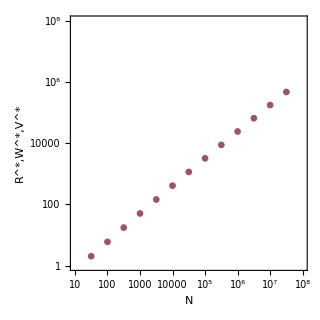

```mathematica
VScalingModelPlot=ListLogLogPlot[Table[{VValues[[i]],ExactModelV/.n->VValues[[i]]},{i,1,Length[VValues]}],PlotRange->{{10^1,10^8},{10^0,10^8}},PlotMarkers->{Graphics[{FaceForm[FinalColors[[1]]],EdgeForm[{FinalColors[[1]],Opacity[opacity]}], Disk[]}],MarkerThickness},Frame->True,AspectRatio->1,FrameLabel->{Style["N",TextSize,FontFamily->"Arial"],Style["R^*,W^*,V^*",TextSize,FontFamily->"Arial"]},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-2,8}],None},{Table[{10^i,Superscript[10,i]},{i,-2,8}],None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.5LinesThickness]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],ImageSize->size]
```

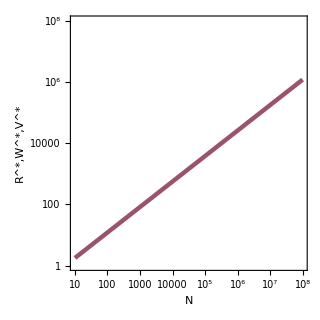

```mathematica
VScalingTheoryPlot=LogLogPlot[AsymptoticsModelV,{n,10^1,10^8},PlotRange->{{10^1,10^8},{10^0,10^8}},PlotStyle->{FinalColors[[1]],Thickness[GraphThickness/2]},Frame->True,AspectRatio->1,FrameLabel->{Style["N",TextSize,FontFamily->"Arial"],Style["R^*,W^*,V^*",TextSize,FontFamily->"Arial"]},FrameTicks->{{Table[{10^i,Superscript[10,i]},{i,-2,8}],None},{Table[{10^i,Superscript[10,i]},{i,-2,8}],None}},FrameTicksStyle->TicksSize,FrameStyle->Directive[Black,Thickness[0.5LinesThickness]],LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->TicksSize],ImageSize->size]
```

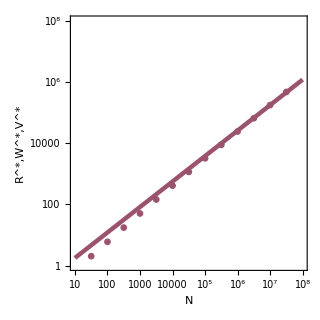

```mathematica
VPlot=Show[VScalingModelPlot,VScalingTheoryPlot]
```

### Scaling of all

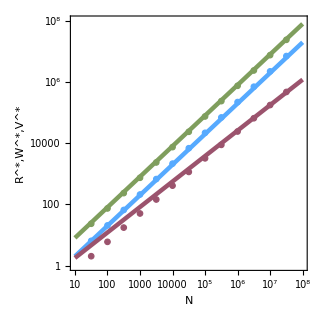

```mathematica
Show[RPlot,WPlot,VPlot]
```

### Steady-state simplification

```mathematica
RSteadyStateSimp
```

(H (-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))-√(H^2 (4 r (v+κ) (-k1 v σ+k2 γ (v+κ+ω))+(-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))^2)))/(2 k1 v σ-2 k2 γ (v+κ+ω))

```mathematica
WSteadyStateSimp
```

((k1 r σ+k2 γ ω) √(H^2 (((r+k2 γ) (v+κ)-k1 v σ)^2+2 ((r (r+v)+k2 (r-v) γ) (v+κ)+k1 v (r+v) σ) ω+(r+v)^2 ω^2))+H (k1 r σ (-((r+k2 γ) (v+κ))+k1 v σ)-(k2 γ (r-k2 γ) (v+κ)+k1 (r (r+v)+k2 (2 r+v) γ) σ) ω-k2 (r+v) γ ω^2))/(2 (k2 γ (v+κ)-k1 (r+v) σ) (-k1 v σ+k2 γ (v+κ+ω)))

```mathematica
VSteadyStateSimp
```

(H (k2 γ (v+κ)+r (v+κ+ω)+v (-k1 σ+ω))-√(H^2 (4 r (v+κ) (-k1 v σ+k2 γ (v+κ+ω))+(-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))^2)))/(2 k2 γ (v+κ)-2 k1 (r+v) σ)

```mathematica
FullSimplify[√(H^2 (4 r (v+κ) (-k1 v σ+k2 γ (v+κ+ω))+(-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))^2))-√(H^2 (4 r (v+κ) (-k1 v σ+k2 γ (v+κ+ω))+(-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))^2))]
```

0

```mathematica
FullSimplify[√(H^2 (((r+k2 γ) (v+κ)-k1 v σ)^2+2 ((r (r+v)+k2 (r-v) γ) (v+κ)+k1 v (r+v) σ) ω+(r+v)^2 ω^2))/√(H^2 (4 r (v+κ) (-k1 v σ+k2 γ (v+κ+ω))+(-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))^2))]
```

1

```mathematica
sqrt=√(H^2 (4 r (v+κ) (k2 γ (v+κ+ω)-k1 v σ)+(v (k1 σ+ω)+r (v+κ+ω)-k2 γ (v+κ))^2))
```

√(H^2 (4 r (v+κ) (-k1 v σ+k2 γ (v+κ+ω))+(-k2 γ (v+κ)+r (v+κ+ω)+v (k1 σ+ω))^2))

#### R

```mathematica
FullSimplify[RSteadyStateSimp-(H (k2 γ (v+κ)-v (k1 σ+ω)-r (v+κ+ω))+sqrt)/(2 k2 γ (v+κ+ω)-2 k1 v σ)]
```

0

#### W

```mathematica
FullSimplify[H (k1 r σ (k1 v σ-((r+k2 γ) (v+κ)))-(k2 γ (r-k2 γ) (v+κ)+k1 (r (r+v)+k2 (2 r+v) γ) σ) ω-k2 (r+v) γ ω^2)]
```

H (k1 r σ (-((r+k2 γ) (v+κ))+k1 v σ)-(k2 γ (r-k2 γ) (v+κ)+k1 (r (r+v)+k2 (2 r+v) γ) σ) ω-k2 (r+v) γ ω^2)

```mathematica
FullSimplify[WSteadyStateSimp-(H (k1 r σ (k1 v σ-((r+k2 γ) (v+κ)))-k2 (r+v) γ ω^2)-H((k2 γ (r-k2 γ) (v+κ)+k1 (r (r+v)+k2 (2 r+v) γ) σ) ω)+(k1 r σ+k2 γ ω)sqrt)/(2 (k2 γ (v+κ)-k1 (r+v) σ) (k2 γ (v+κ+ω)-k1 v σ))]
```

0

#### V

```mathematica
FullSimplify[VSteadyStateSimp-(H (k2 γ (v+κ)+r (v+κ+ω)+v (ω-k1 σ))-sqrt)/(2 k2 γ (v+κ)-2 k1 (r+v) σ)]
```

0